```mathematica
AutoCollapse[]:=(If[$FrontEnd=!=$Failed,SelectionMove[EvaluationNotebook[],All,GeneratedCell];
FrontEndTokenExecute["SelectionCloseUnselectedCells"]]);

Button[Style["Clear All Output",FontFamily->"Consolas", FontWeight->"Thin",FontSize->12],
FrontEndExecute[FrontEndToken["DeleteGeneratedCells"]];
NotebookLocate["PrimitiveInitialization"];
SelectionEvaluate[EvaluationNotebook[]]
]
AutoCollapse[]
```

Clear All Output

```mathematica
Button["Perform Basic Initialization",NotebookLocate["InitializationCell"]
SelectionEvaluate[EvaluationNotebook[]]]
AutoCollapse[];
```

Perform Basic Initialization

```mathematica
Button["Define Theoretical Vectors and Tensors",NotebookLocate["CurvilinearTheoreticalQuantities"]
SelectionEvaluate[EvaluationNotebook[]]]
AutoCollapse[];
```

Define Theoretical Vectors and Tensors

```mathematica
Button["Define Numerical Subroutines",NotebookLocate["NumericalSubroutines"]
SelectionEvaluate[EvaluationNotebook[]]]
AutoCollapse[];
```

Define Numerical Subroutines

```mathematica
Button["Define Geometry, Mesh, FEA Data structures Subroutines",NotebookLocate["GeometryMeshDataStructures"]
SelectionEvaluate[EvaluationNotebook[]]]
AutoCollapse[];
```

Define Geometry, Mesh, FEA Data structures Subroutines

```mathematica
Button["Execute Solve Subroutines",NotebookLocate["SolveSubroutines"]
SelectionEvaluate[EvaluationNotebook[]]]
AutoCollapse[];
```

Execute Solve Subroutines

```mathematica
Button["Compute Numerical Stress and Strain",NotebookLocate["PostProcessingSubroutines"]
SelectionEvaluate[EvaluationNotebook[]]]
AutoCollapse[];
```

Compute Numerical Stress and Strain

## Initialization

```mathematica
Unprotect["Global`*"];
Clear["Global`*"];
ClearAll["Global`*"] ;
Remove["Global`*"] ;
<<Notation`;
Off[Symbolize::bsymbexs];
Off[Remove::rmnsm];
AutoCollapse[]:=(If[$FrontEnd=!=$Failed,SelectionMove[EvaluationNotebook[],All,GeneratedCell];
FrontEndTokenExecute["SelectionCloseUnselectedCells"]]);
Print["Variable Cleared"];
AutoCollapse[];
```

Variable Cleared

```mathematica
Symbolize[Subscript[u, ρ]]; Symbolize[Subscript[u, ϕ]]; Symbolize[Subscript[u, ζ]]; 
Symbolize[Subscript[u, a]^ρ];Symbolize[Subscript[u, a]^ϕ];Symbolize[Subscript[u, a]^ζ];
Symbolize[Subscript[u, b]^ρ];Symbolize[Subscript[u, b]^ϕ];Symbolize[Subscript[u, b]^ζ];
Symbolize[u^ρ]; Symbolize[u^ϕ]; Symbolize[u^ζ];
Symbolize[w^ρ]; Symbolize[w^ϕ]; Symbolize[w^ζ];
Symbolize[Subscript[w, ρ]]; Symbolize[Subscript[w, ϕ]]; Symbolize[Subscript[w, ζ]];
 Symbolize[N^𝔄]Symbolize[N^𝔅]Symbolize[N^ℭ];Symbolize[N^𝔇]Symbolize[N^𝔈]Symbolize[N^𝔉];
Symbolize[(U⃗)_n];Symbolize[(X⃗)_r];Symbolize[(U⃗)^n];Symbolize[X⃗];Symbolize[τ^n];
Symbolize[Subscript[a, ρ,𝔄]];Symbolize[Subscript[a, ϕ,𝔅]];Symbolize[Subscript[a, ζ,ℭ]];
Symbolize[Subscript[b, ρ,𝔇]];Symbolize[Subscript[b, ϕ,𝔈]];Symbolize[Subscript[b, ζ,𝔉]]
Symbolize[L̄];
 Notation[g_(i_·j_·)   ⟺  CoVarMetricCoeffs[[i_,j_]]]
Notation[g^(i_·j_·)   ⟺  ContraVarMetricCoeffs[[i_,j_]]]
Notation[Γ_(i_·j_·)^(k_·)   ⟺  Γ[[i_,j_,k_]]]
Notation[w^(i_·)   ⟺  ContraVarDispW[[i_]]]
Notation[u^(i_·)   ⟺  ContraVarDispU[[i_]]]
Notation[u_(i_·)   ⟺  CoVarDispU[[i_]]]
Notation[x^(i_·)   ⟺  Coords[[i_]]]
Notation[w_(j_·)   ⟺  CoVarDispW[[j_]]]
Notation[u^(i_·)|_(j_·)  ⟺  CovariantDU1[i_,j_]]
Notation[u_(i_·)|_(j_·)  ⟺  CovariantDU2[i_,j_]]
Notation[w^(i_·)|_(j_·)  ⟺  CovariantDW1[i_,j_]]
Notation[w_(i_·)|_(j_·)  ⟺  CovariantDW2[i_,j_]]
Notation[γ_(i_·j_·)   ⟺  StrainCovariantU[[i_,j_]]]
Notation[ϵ_(i_·j_·)   ⟺  StrainCovariantW[[i_,j_]]]
Notation[𝔼^(i_·j_·k_·l_·)   ⟺  StiffnessContra[[i_,j_,k_,l_]]]
Notation[(∂u_)/(∂x_)   ⟺  D[u_,x_]]
Notation[τ^(i_·j_·)   ⟺  StressContra[[i_,j_]]]
Symbolize[x_^h];Symbolize[x_^e];
Symbolize[Subscript[U, 1]^n];Symbolize[Subscript[U, 2]^n];Symbolize[Subscript[U, 3]^n]
Symbolize[Subscript[U, n]^1];Symbolize[Subscript[U, n]^2];Symbolize[Subscript[U, n]^3]
Symbolize[Subscript[u, ρ]^h];Symbolize[Subscript[u, ϕ]^h];Symbolize[Subscript[u, ζ]^h]
Symbolize[Subscript[η, g]];Symbolize[Subscript[n, x_]];
Symbolize[N^(i_)];Symbolize[N_(,x_)^(i_)];Symbolize[Subscript[x_, i_]];Symbolize[(x⃗)^h];
Symbolize[(f⃗)_(e,a)];
Symbolize[Subscript[Π, e]];
Symbolize[(J^e)^-1];
Symbolize[x̲];
Symbolize[Subscript[u, ρ,ρ]^h];Symbolize[Subscript[u, ϕ,ρ]^h];Symbolize[Subscript[u, ζ,ρ]^h];
Symbolize[Subscript[u, ρ,ζ]^h]; Symbolize[Subscript[u, ϕ,ζ]^h];Symbolize[Subscript[u, ζ,ζ]^h];  
Symbolize[Subscript[u, h]^(ρ,ρ)];Symbolize[Subscript[u, h]^(ϕ,ρ)];Symbolize[Subscript[u, h]^(ζ,ρ)];
Symbolize[Subscript[u, h]^(ρ,ζ)]; Symbolize[Subscript[u, h]^(ϕ,ζ)];Symbolize[Subscript[u, h]^(ζ,ζ)];  
Symbolize[Subscript[u, ρ]^h];  Symbolize[Subscript[u, ϕ]^h];  Symbolize[Subscript[u, ζ]^h];  
Symbolize[Subscript[u, h]^ρ]; Symbolize[Subscript[u, h]^ϕ] ;Symbolize[Subscript[u, h]^ζ];
Symbolize[Subscript[σ, ρ]^ρ];Symbolize[Subscript[σ, ϕ]^ρ];Symbolize[Subscript[σ, ζ]^ρ];
Symbolize[Subscript[σ, ρ]^ζ];Symbolize[Subscript[σ, ϕ]^ζ];Symbolize[Subscript[σ, ζ]^ζ];
Print["New Symbols Defined"]
AutoCollapse[]
```

New Symbols Defined

```mathematica
<<HaneeshPackages`
PrntRls={Subscript[u, 1]-> Subscript[u,1],Subscript[u, 2]-> Subscript[u,2],Subscript[u, 3]-> Subscript[u,3],
Subscript[x, 1]-> Subscript[x,1],Subscript[x, 2]-> Subscript[x,2],Subscript[x, 3]-> Subscript[x,3],
Subscript[u, a]^ρ->Subsuperscript[u,a,ρ],Subscript[u, a]^ϕ->Subsuperscript[u,a,ϕ],Subscript[u, a]^ζ->Subsuperscript[u,a,ζ],
u^ρ-> Superscript[u,ρ],u^ϕ-> Superscript[u,ϕ],u^ζ-> Superscript[u,ζ],
w^ρ-> Superscript[w,ρ],w^ϕ-> Superscript[w,ϕ],w^ζ-> Superscript[w,ζ],
Subscript[u, ρ]-> Subscript[u,ρ],Subscript[u, ϕ]-> Subscript[u,ϕ],Subscript[u, ζ]-> Subscript[u,ζ],
N^𝔄-> Superscript[N,𝔄],N^𝔅-> Superscript[N,𝔅],N^ℭ-> Superscript[N,ℭ],
N^𝔇-> Superscript[N,𝔇],N^𝔈-> Superscript[N,𝔈],N^𝔉-> Superscript[N,𝔉],N^(a)-> Superscript[N,"(a)"],N^(b)-> Superscript[N,"(b)"],
Subscript[a, ρ, 𝔄]-> Subscript[a,ρ,𝔄],Subscript[a, ϕ, 𝔅]-> Subscript[a,ϕ,𝔅],Subscript[a, ζ, ℭ]-> Subscript[a,ζ,ℭ],
Subscript[b, ρ, 𝔇]-> Subscript[b,ρ,𝔇],Subscript[b, ϕ, 𝔈]-> Subscript[b,ϕ,𝔈],Subscript[b, ζ, 𝔉]-> Subscript[b,ζ,𝔉],N_(,ζ)^(a)->Subsuperscript[N,",ζ","(a)"],N_(,ρ)^(a)->Subsuperscript[N,",ρ","(a)"],N_(,ζ)^(b)->Subsuperscript[N,",ζ","(b)"],N_(,ρ)^(b)->Subsuperscript[N,",ρ","(b)"],
Subscript[w, ρ]-> Subscript[w,ρ],Subscript[w, ϕ]-> Subscript[w,ϕ],Subscript[w, ζ]-> Subscript[w,ζ],
L̄->Overscript[L,_],Subscript[ΔT, 0]-> Subscript[ΔT,0]
};
GenerateMonoSubSuperscriptRules[]:=Module[{body, ww,zz,xx,yy,Prules1,Prules2,scripts},
body=Join[Alphabet["Greek"],Alphabet[],ToUpperCase[Alphabet[]],ToUpperCase[Alphabet["Greek"]]];
scripts=Join[Table[ToString[i],{i,1,9}],List@ToString[ϕ],Map[ToString,Alphabet["Greek"]]];
xx=Flatten@Outer[StringJoin,Map[ToString,body],{"⎵Subscript⎵"},scripts];
xx=Map[Symbol,xx];
yy=Flatten@Outer[Subscript,body,scripts];
Prules1=Table[xx[[i]]->yy[[i]],{i,1,Length@xx}];
ww=Flatten@Outer[StringJoin,Map[ToString,body],{"⎵Superscript⎵"},scripts];
ww=Map[Symbol,ww];
zz=Flatten@Outer[Superscript,body,scripts];
Prules2=Table[ww[[i]]->zz[[i]],{i,1,Length@xx}];
Join[Prules1,Prules2]]
(*PrntRls=Join[PrntRls,GenerateMonoSubSuperscriptRules[]];*)
Pprint[expri_]:=Module[{expr=expri},
expr/.PrntRls//MatrixForm//pdConv
];
Pprint[expri_,title_]:=Module[{expr=expri},
(title=expr)/.PrntRls//MatrixForm//pdConv
];
Print["Print Subroutines Defined"]
AutoCollapse[]
```

Print Subroutines Defined

```mathematica
Subscript[u, ρ]::usage="Covariant component of the displacement in the g^ρ direction (symbol)";
Subscript[u, ϕ]::usage="Covariant component of the displacement in the g^ϕ direction ";
Subscript[u, ζ]::usage="Covariant component of the displacement in the g^ζ direction ";

λ::usage="Lame constant (double)";
μ::usage="Lame constant (double)";
Subscript[ρ, 0]::usage="inner radius (double)";
Subscript[ρ, 1]::usage="outer radius (double)";
Subscript[ζ, 0]::usage="curvilinear coordinate ζ's lower bound(double)";
Subscript[ζ, 1]::usage="curvilinear coordinate ζ's upper bound(double)";
αΔT::usage="α=Coefficient of thermal expansion; ΔT=Temperature change function";

Subscript[n, el]::usage="\tNumber of Finite Elements";
Subscript[n, np]::usage="Number of Finite Element Nodes";
Subscript[n, dof]::usage="Number of degrees of freedom per node";
Subscript[n, en]::usage="Number of nodes per finite element";
Subscript[n, eq]::usage="Total Number of Equations";
Subscript[n, guass]:: usage="Number of integration points";
(x⃗)^h::usage="{ρ_A, ζ_A} = (x⃗)^h⟦A⟧\n A = Global node number\n {ρ_A, ζ_A}= Nodal co-ordinates\n Dimensions[(x⃗)^h]= n_npX n_sd ";
Subscript[n, sd]::usage="Number of space dimensions";
(*Data Structure Arrays*)

SetUpIDArray::usage="Call as SetUpIDArray[]. Will return the ID array";
IEN::usage="IEN(a,e) = A\n\n\ta = Local Node Number\n\te = Element Number\n\tA = Global Node Number";
ID::usage="Dimensions[ID]={n_dof,n_np}\n  
ID[i,A]=Piecewise[{{P,, A∈η-η_g}, {0, A∈η-η_g_i}}]
";
<<NDSolve`FEM`
Guass = N@{{0.308642,{-√3/5,-√3/5}},{0.493827,{0.0,-√3/5}},{0.308642,{√3/5,-√3/5}},{0.493827,{-√3/5,0.0}},{0.790123,{0.0,0.0}},{0.493827,{√3/5,0.0}},{0.308642,{-√3/5,√3/5}},{0.493827,{0.0,√3/5}},{0.308642,{√3/5,√3/5}}};
(N^(1))[ξ_,η_]=1/4(1-ξ)(1-η)(-ξ-η-1);
(N^(2))[ξ_,η_]=1/4(1+ξ)(1-η)(ξ-η-1);
(N^(3))[ξ_,η_]=1/4(1+ξ)(1+η)(ξ+η-1);
(N^(4))[ξ_,η_]=1/4(1-ξ)(1+η)(-ξ+η-1);
(N^(5))[ξ_,η_]=1/2(1-ξ^2)(1-η);
(N^(6))[ξ_,η_]=1/2(1+ξ)(1-η^2);
(N^(7))[ξ_,η_]=1/2(1-ξ^2)(1+η);
(N^(8))[ξ_,η_]=1/2(1-ξ)(1-η^2);
(N_(,ξ)^(1))[ξ_,η_]=D[(N^(1))[ξ,η],ξ];
(N_(,η)^(1))[ξ_,η_]=D[(N^(1))[ξ,η],η];
(N_(,ξ)^(2))[ξ_,η_]=D[(N^(2))[ξ,η],ξ];
(N_(,η)^(2))[ξ_,η_]=D[(N^(2))[ξ,η],η];
(N_(,ξ)^(3))[ξ_,η_]=D[(N^(3))[ξ,η],ξ];
(N_(,η)^(3))[ξ_,η_]=D[(N^(3))[ξ,η],η];
(N_(,ξ)^(4))[ξ_,η_]=D[(N^(4))[ξ,η],ξ];
(N_(,η)^(4))[ξ_,η_]=D[(N^(4))[ξ,η],η];
(N_(,ξ)^(5))[ξ_,η_]=D[(N^(5))[ξ,η],ξ];
(N_(,η)^(5))[ξ_,η_]=D[(N^(5))[ξ,η],η];
(N_(,ξ)^(6))[ξ_,η_]=D[(N^(6))[ξ,η],ξ];
(N_(,η)^(6))[ξ_,η_]=D[(N^(6))[ξ,η],η];
(N_(,ξ)^(7))[ξ_,η_]=D[(N^(7))[ξ,η],ξ];
(N_(,η)^(7))[ξ_,η_]=D[(N^(7))[ξ,η],η];
(N_(,ξ)^(8))[ξ_,η_]=D[(N^(8))[ξ,η],ξ];
(N_(,η)^(8))[ξ_,η_]=D[(N^(8))[ξ,η],η];
Print["Nomenclature defined"]
AutoCollapse[]
```

Nomenclature defined

## Problem Formulations: Theory

```mathematica
Γ=Table[0,{i,1,3},{j,1,3},{k,1,3}];
Γ[[;;,;;,1]]={{0,0,0},{0,-ρ,0},{0,0,0}};
Γ[[;;,;;,2]]={{0,1/ρ,0},{1/ρ,0,0},{0,0,0}};
Γ[[;;,;;,3]]={{0,-(L̄)/ρ,0},{-(L̄)/ρ,0,0},{0,0,0}};
(*"Christoffel"<>" Symbols"*)
Echo[Γ//MatrixForm//Pprint,"Christoffel Symbols components"];
AutoCollapse[]
```

Christoffel Symbols components ((0
0
0) | (0
1/ρ
-(L̄)/ρ) | (0
0
0)
(0
1/ρ
-(L̄)/ρ) | (-ρ
0
0) | (0
0
0)
(0
0
0) | (0
0
0) | (0
0
0))

```mathematica
CoVarMetricCoeffs=Table[0,{i,1,3},{j,1,3}];
CoVarMetricCoeffs={{1,0,0},{0,ρ^2+(L̄)^2,L̄},{0,L̄,1}};
ContraVarMetricCoeffs={{1,0,0},{0,1/ρ^2,-(L̄)/ρ^2},{0,-(L̄)/ρ^2,(ρ^2+(L̄)^2)/ρ^2}};
1
Echo[Table[g_(i·j·),{i,1,3},{j,1,3}]//Pprint,"Metric Tensor, Covariant  components: "];
Echo[Table[g^(i·j·),{i,1,3},{j,1,3}]//Pprint,"Metric Tensor, Contravariant  components: "];

AutoCollapse[]
```

1

Metric Tensor, Covariant  components:  (1 | 0 | 0
0 | (L̄)^2+ρ^2 | L̄
0 | L̄ | 1)

Metric Tensor, Contravariant  components:  (1 | 0 | 0
0 | 1/ρ^2 | -(L̄)/ρ^2
0 | -(L̄)/ρ^2 | ((L̄)^2+ρ^2)/ρ^2)

```mathematica
2
Coords={ρ,ϕ,ζ};
ContraVarDispU={Subscript[a, ρ,𝔄](N^𝔄)[ρ,ζ],Subscript[a, ϕ,𝔅](N^𝔅)[ρ,ζ],Subscript[a, ζ,ℭ](N^ℭ)[ρ,ζ]}; 
ContraVarDispW={Subscript[b, ρ,𝔇](N^𝔇)[ρ,ζ],Subscript[b, ϕ,𝔈](N^𝔈)[ρ,ζ],Subscript[b, ζ,𝔉](N^𝔉)[ρ,ζ]}; 

(*ContraVarDispU={u^ρ[ρ,ζ],u^ϕ[ρ,ζ],u^ζ[ρ,ζ]}; 
ContraVarDispW={w^ρ[ρ,ζ],w^ϕ[ρ,ζ],w^ζ[ρ,ζ]};
*)
CoVarDispU=Table[∑_(j=1)^3 (g_(i·j·)u^(j·)),{i,1,3}];
CoVarDispW=Table[∑_(j=1)^3 (g_(i·j·)w^(j·)),{i,1,3}];


Echo[Table[x^(i·),{i,1,3}]//Pprint,"Co-ordinates \n"];
Echo[Table[u_(i·),{i,1,3}]//Pprint,"Covariant components of the displacement vector \n"];
Echo[Table[u^(i·),{i,1,3}]//Pprint,"Contravariant components of the displacement vector \n"];
Echo[Table[w_(i·),{i,1,3}]//Pprint,"Covariant components of the displacement variation  vector \n"];
Echo[Table[w^(i·),{i,1,3}]//Pprint,"Contravariant components of the displacement variation  vector \n"];
AutoCollapse[]
```

2

Co-ordinates 
 (ρ
ϕ
ζ)

Covariant components of the displacement vector 
 (a_(ρ,𝔄) N^𝔄(ρ,ζ)
((L̄)^2+ρ^2) a_(ϕ,𝔅) N^𝔅(ρ,ζ)+L̄ a_(ζ,ℭ) N^ℭ(ρ,ζ)
L̄ a_(ϕ,𝔅) N^𝔅(ρ,ζ)+a_(ζ,ℭ) N^ℭ(ρ,ζ))

Contravariant components of the displacement vector 
 (a_(ρ,𝔄) N^𝔄(ρ,ζ)
a_(ϕ,𝔅) N^𝔅(ρ,ζ)
a_(ζ,ℭ) N^ℭ(ρ,ζ))

Covariant components of the displacement variation  vector 
 (b_(ρ,𝔇) N^𝔇(ρ,ζ)
((L̄)^2+ρ^2) b_(ϕ,𝔈) N^𝔈(ρ,ζ)+L̄ b_(ζ,𝔉) N^𝔉(ρ,ζ)
L̄ b_(ϕ,𝔈) N^𝔈(ρ,ζ)+b_(ζ,𝔉) N^𝔉(ρ,ζ))

Contravariant components of the displacement variation  vector 
 (b_(ρ,𝔇) N^𝔇(ρ,ζ)
b_(ϕ,𝔈) N^𝔈(ρ,ζ)
b_(ζ,𝔉) N^𝔉(ρ,ζ))

```mathematica
CovariantDU2[i_,j_]:=((∂u_(i·))/(∂x^(j·))-∑_(k=1)^3 (u_(k·)Γ_(i·j·)^(k·)));
StrainCovariantU=Table[1/2((u_(i·)|_(j·))+(u_(j·)|_(i·))),{i,1,3},{j,1,3}];

CovariantDW2[i_,j_]:=((∂w_(i·))/(∂x^(j·))-∑_(k=1)^3 (w_(k·)Γ_(i·j·)^(k·)));
StrainCovariantW=Table[1/2((w_(i·)|_(j·))+(w_(j·)|_(i·))),{i,1,3},{j,1,3}];

Print["Strain Tensors"]
{FullSimplify@Table[γ_(i·j·),{i,1,3},{j,1,3}]//Pprint(*,Flatten@FullSimplify@Table[ϵ_(i·j·),{i,1,3},{j,1,3}]//Pprint*)}
AutoCollapse[]
```

Strain Tensors

{(a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ρ) | 1/2 (((L̄)^2+ρ^2) a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ρ)+L̄ a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ρ)) | 1/2 (L̄ a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ρ)+a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ζ)+a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ρ))
1/2 (((L̄)^2+ρ^2) a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ρ)+L̄ a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ρ)) | ρ a_(ρ,𝔄) N^𝔄(ρ,ζ) | 1/2 (((L̄)^2+ρ^2) a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ζ)+L̄ a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ζ))
1/2 (L̄ a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ρ)+a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ζ)+a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ρ)) | 1/2 (((L̄)^2+ρ^2) a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ζ)+L̄ a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ζ)) | L̄ a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ζ)+a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ζ))}

```mathematica
Unprotect[StiffnessContra];
ClearAll[StiffnessContra];

StiffnessContra=μ Table[g^(i·r·) g^(j·s·)+g^(i·s·) g^(j·r·)+λ/μ g^(i·j·)g^(r·s·),{i,1,3},{j,1,3},{r,1,3},{s,1,3}];
Protect[StiffnessContra];
Print["Stiffness Defined"]
AutoCollapse[]
```

Stiffness Defined

```mathematica
StressContra=Table[∑_(r=1)^3 ∑_(s=1)^3 𝔼^(i·j·r·s·)(γ_(r·s·)-αΔT[ρ,ζ] g_(r·s·)),{i,1,3},{j,1,3}];
Print["Stress Defined"]
Print["Stress Tensors"]
{FullSimplify@Table[τ^(i·j·),{i,1,3},{j,1,3}]//Pprint}
AutoCollapse[]
```

Stress Defined

Stress Tensors

{((λ+2 μ) a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ρ)+(λ a_(ρ,𝔄) N^𝔄(ρ,ζ))/ρ+λ a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ζ)-(3 λ+2 μ) αΔT(ρ,ζ) | μ a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ρ)-(μ L̄ a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ζ))/ρ^2 | (μ ((L̄)^2+ρ^2) a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ζ))/ρ^2+μ a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ρ)
μ a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ρ)-(μ L̄ a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ζ))/ρ^2 | (ρ (-2 μ L̄ a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ζ)+λ a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ρ)+λ a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ζ)-(3 λ+2 μ) αΔT(ρ,ζ))+(λ+2 μ) a_(ρ,𝔄) N^𝔄(ρ,ζ))/ρ^3 | (ρ (-L̄ (λ a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ρ)+(λ+μ) a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ζ))+μ ((L̄)^2+ρ^2) a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ζ)+L̄ (3 λ+2 μ) αΔT(ρ,ζ))-L̄ (λ+2 μ) a_(ρ,𝔄) N^𝔄(ρ,ζ))/ρ^3
(μ ((L̄)^2+ρ^2) a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ζ))/ρ^2+μ a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ρ) | (ρ (-L̄ (λ a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ρ)+(λ+μ) a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ζ))+μ ((L̄)^2+ρ^2) a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ζ)+L̄ (3 λ+2 μ) αΔT(ρ,ζ))-L̄ (λ+2 μ) a_(ρ,𝔄) N^𝔄(ρ,ζ))/ρ^3 | (a_(ρ,𝔄) ((L̄)^2 (λ+2 μ)+λ ρ^2) N^𝔄(ρ,ζ)-ρ ((L̄)^2+ρ^2) (-λ a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ρ)-(λ+2 μ) a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ζ)+(3 λ+2 μ) αΔT(ρ,ζ)))/ρ^3)}

```mathematica
W=FullSimplify@Sum[τ^(i·j·)ϵ_(i·j·),{i,1,3},{j,1,3}];
Print["Strain Energy Density"]
AutoCollapse[]
```

```mathematica
Patt={
 x_[ρ,ζ] Derivative[0,1][(y_)][ρ,ζ],
x_[ρ,ζ] Derivative[1,0][(y_)][ρ,ζ],Derivative[1,0][(x_)][ρ,ζ]Derivative[1,0][(y_)][ρ,ζ],
Derivative[0,1][(x_)][ρ,ζ]Derivative[0,1][(y_)][ρ,ζ],
Derivative[0,1][(x_)][ρ,ζ]Derivative[1,0][(y_)][ρ,ζ]
x_[ρ,ζ] y_[ρ,ζ]};

Print[Style["Global Stiffness Matrix",Orange]]
K=Simplify@Outer[D[W ,#1,#2]&,{Subscript[a, ρ,𝔄],Subscript[a, ϕ,𝔅],Subscript[a, ζ,ℭ]},{Subscript[b, ρ,𝔇],Subscript[b, ϕ,𝔈],Subscript[b, ζ,𝔉]}];
Flatten@Table[Collect[Expand@K[[i,j]],Patt,Simplify],{i,1,3},{j,1,3}]//Pprint
AutoCollapse[]
```

```mathematica
F=Simplify@Map[D[(-W /.{Subscript[a, ρ,𝔄]->0,Subscript[a, ϕ,𝔅]->0,Subscript[a, ζ,ℭ]->0}),#]&,{Subscript[b, ρ,𝔇],Subscript[b, ϕ,𝔈],Subscript[b, ζ,𝔉]}];
Print[Style["Global Force Matrix",Orange]]
Flatten@Table[Collect[Expand@F[[i]],Patt,Simplify],{i,1,3}]//Pprint
AutoCollapse[]
```

Global to Local Transformation

```mathematica
K/.((Derivative[0,1][(N^𝔄)])[ρ,ζ] | (Derivative[0,1][(N^𝔅)])[ρ,ζ] | (Derivative[0,1][(N^ℭ)])[ρ,ζ])-> (N_(,ζ)^(a))[ξ,η]/.((Derivative[1,0][(N^𝔄)])[ρ,ζ] | (Derivative[1,0][(N^𝔅)])[ρ,ζ] | (Derivative[1,0][(N^ℭ)])[ρ,ζ])-> (N_(,ρ)^(a))[ξ,η]/.((N^𝔄)[ρ,ζ]| (N^𝔅)[ρ,ζ] | (N^ℭ)[ρ,ζ])->(N^(a))[ξ,η]/.((Derivative[0,1][(N^𝔇)])[ρ,ζ]| (Derivative[0,1][(N^𝔈)])[ρ,ζ] | (Derivative[0,1][(N^𝔉)])[ρ,ζ])-> (N_(,ζ)^(b))[ξ,η]/.((Derivative[1,0][(N^𝔇)])[ρ,ζ]| (Derivative[1,0][(N^𝔈)])[ρ,ζ] | (Derivative[1,0][(N^𝔉)])[ρ,ζ])-> (N_(,ρ)^(b))[ξ,η]/.((N^𝔇)[ρ,ζ]| (N^𝔈)[ρ,ζ] | (N^𝔉)[ρ,ζ])->(N^(b))[ξ,η]
AutoCollapse[]
```

```mathematica
F/.((Derivative[0,1][(N^𝔄)])[ρ,ζ] | (Derivative[0,1][(N^𝔅)])[ρ,ζ] | (Derivative[0,1][(N^ℭ)])[ρ,ζ])-> (N_(,ζ)^(a))[ξ,η]/.((Derivative[1,0][(N^𝔄)])[ρ,ζ] | (Derivative[1,0][(N^𝔅)])[ρ,ζ] | (Derivative[1,0][(N^ℭ)])[ρ,ζ])-> (N_(,ρ)^(a))[ξ,η]/.((N^𝔄)[ρ,ζ]| (N^𝔅)[ρ,ζ] | (N^ℭ)[ρ,ζ])->(N^(a))[ξ,η]/.((Derivative[0,1][(N^𝔇)])[ρ,ζ]| (Derivative[0,1][(N^𝔈)])[ρ,ζ] | (Derivative[0,1][(N^𝔉)])[ρ,ζ])-> (N_(,ζ)^(b))[ξ,η]/.((Derivative[1,0][(N^𝔇)])[ρ,ζ]| (Derivative[1,0][(N^𝔈)])[ρ,ζ] | (Derivative[1,0][(N^𝔉)])[ρ,ζ])-> (N_(,ρ)^(b))[ξ,η]/.((N^𝔇)[ρ,ζ]| (N^𝔈)[ρ,ζ] | (N^𝔉)[ρ,ζ])->(N^(b))[ξ,η]
AutoCollapse[]
```

## Problem Solution: Numerics

### Numerics subroutine:

```mathematica
Print[Text[Style["Defined SetUpη_g",Orange]]]
ClearAll[Subscript[SetUpη, g]];
Subscript[SetUpη, g][Coordinates0_,tol_:0.0001]:=Module[{Coordinates=Coordinates0,Subscript[n, np], Subscript[ρ, i],Subscript[ζ, i],Subscript[η, g]},
Subscript[n, np]=Length@Coordinates;
Subscript[η, g]={{},{},{}};
For[i=1,i≤Subscript[n, np],i++,
{Subscript[ρ, i],Subscript[ζ, i]}=Coordinates[[i]];
If[Abs[Subscript[ζ, i]-Subscript[ζ, 0]]≤   tol,AppendTo[Subscript[η, g][[2]],i]; AppendTo[Subscript[η, g][[3]],i]];
];
Subscript[η, g] 
] 
AutoCollapse[]
```

Defined SetUpη_g

```mathematica
Unprotect[SetUpIDArray];
ClearAll[SetUpIDArray];
SetUpIDArray[]:=Module[{P,A,i,ID},
ID=Table[0,{i,1,Subscript[n, dof]},{j,1,Subscript[n, np]}];
P=1;
For[A=1,A≤ Subscript[n, np],A++,
For[i=1,i≤ Subscript[n, dof],i++,
If[!MemberQ[Subscript[η, g][[i]],A],ID[[i,A]]=P;P=P+1,ID[[i,A]]=0];
];
];
ID
]
Protect[SetUpIDArray];
Print[Text[Style["Defined SetUpIDArray",Orange]]]
AutoCollapse[]
```

Defined SetUpIDArray

```mathematica
Unprotect[k^e];
ClearAll[k^e];(k^e)[{ξ_,η_},{ρ_,ζ_}]:={{1/ρ^2(μ ((L̄)^2+ρ^2) (N_(,ζ)^(a))[ξ,η] (N_(,ζ)^(b))[ξ,η]+ρ (N_(,ρ)^(a))[ξ,η] ((λ+2 μ) ρ (N_(,ρ)^(b))[ξ,η]+λ (N^(b))[ξ,η])+(N^(a))[ξ,η] (λ ρ (N_(,ρ)^(b))[ξ,η]+(λ+2 μ) (N^(b))[ξ,η])),-(2 L̄ μ (N_(,ζ)^(b))[ξ,η] (N^(a))[ξ,η])/ρ,λ (N_(,ζ)^(b))[ξ,η] (N_(,ρ)^(a))[ξ,η]+μ (N_(,ζ)^(a))[ξ,η] (N_(,ρ)^(b))[ξ,η]+(λ (N_(,ζ)^(b))[ξ,η] (N^(a))[ξ,η])/ρ},{-(2 L̄ μ (N_(,ζ)^(a))[ξ,η] (N^(b))[ξ,η])/ρ,(μ ((L̄)^2+ρ^2) (((L̄)^2+ρ^2) (N_(,ζ)^(a))[ξ,η] (N_(,ζ)^(b))[ξ,η]+ρ^2 (N_(,ρ)^(a))[ξ,η] (N_(,ρ)^(b))[ξ,η]))/ρ^2,(L̄ μ (((L̄)^2+ρ^2) (N_(,ζ)^(a))[ξ,η] (N_(,ζ)^(b))[ξ,η]+ρ^2 (N_(,ρ)^(a))[ξ,η] (N_(,ρ)^(b))[ξ,η]))/ρ^2},{μ (N_(,ζ)^(b))[ξ,η] (N_(,ρ)^(a))[ξ,η]+λ (N_(,ζ)^(a))[ξ,η] (N_(,ρ)^(b))[ξ,η]+(λ (N_(,ζ)^(a))[ξ,η] (N^(b))[ξ,η])/ρ,(L̄ μ (((L̄)^2+ρ^2) (N_(,ζ)^(a))[ξ,η] (N_(,ζ)^(b))[ξ,η]+ρ^2 (N_(,ρ)^(a))[ξ,η] (N_(,ρ)^(b))[ξ,η]))/ρ^2,(((L̄)^2 μ+(λ+2 μ) ρ^2) (N_(,ζ)^(a))[ξ,η] (N_(,ζ)^(b))[ξ,η]+μ ρ^2 (N_(,ρ)^(a))[ξ,η] (N_(,ρ)^(b))[ξ,η])/ρ^2}}
Protect[k^e];
Print[Text[Style["Defined k^e",Orange]]]
AutoCollapse[]
```

Defined k^e

```mathematica
Unprotect[f^e];
ClearAll[f^e];
(f^e)[{ξ_,η_},{ρ_,ζ_}]:={((3 λ+2 μ) (ρ (N_(,ρ)^(b))[ξ,η]+(N^(b))[ξ,η]) αΔT[ρ,ζ])/ρ,0,(3 λ+2 μ) (N_(,ζ)^(b))[ξ,η] αΔT[ρ,ζ]}

Protect[f^e];
Print[Text[Style["Defined f^e",Orange]]]
AutoCollapse[]
```

Defined f^e

```mathematica
Unprotect[CalculateGuassPoints];
ClearAll[CalculateGuassPoints];

CalculateGuassPoints[e0_]:=Module[{e=e0,P,Q,R,S,T,U,V,W,Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6],Subscript[x, 7],Subscript[x, 8],Subscript[x, 9],Subscript[y, 1],Subscript[y, 2],Subscript[y, 3],Subscript[y, 4],Subscript[y, 5],Subscript[y, 6],Subscript[y, 7],Subscript[y, 8],Subscript[y, 9],GuassPointsSpatial,GuassPointsNatural,GuassWeights,i,Subscript[w, i],Subscript[ξ, i],Subscript[η, i],Subscript[ρ, i],Subscript[ζ, i]},
{P,Q,R,S,T,U,V,W}=IEN[[;;,e]];
{{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]},{Subscript[x, 3],Subscript[y, 3]},{Subscript[x, 4],Subscript[y, 4]},{Subscript[x, 5],Subscript[y, 5]},{Subscript[x, 6],Subscript[y, 6]},{Subscript[x, 7],Subscript[y, 7]},{Subscript[x, 8],Subscript[y, 8]}}=((x⃗)^h)[[{P,Q,R,S,T,U,V,W}]];
GuassWeights={};
GuassPointsSpatial={};
GuassPointsNatural={};
For[i=1,i≤ Subscript[n, guass],i++,
{Subscript[w, i],{Subscript[ξ, i],Subscript[η, i]}}=Guass[[i]];
{Subscript[ρ, i],Subscript[ζ, i]}={(N^(1))[Subscript[ξ, i],Subscript[η, i]] Subscript[x, 1]+(N^(2))[Subscript[ξ, i],Subscript[η, i]] Subscript[x, 2]+(N^(3))[Subscript[ξ, i],Subscript[η, i]] Subscript[x, 3]+(N^(4))[Subscript[ξ, i],Subscript[η, i]] Subscript[x, 4]+(N^(5))[Subscript[ξ, i],Subscript[η, i]] Subscript[x, 5]+(N^(6))[Subscript[ξ, i],Subscript[η, i]] Subscript[x, 6]+(N^(7))[Subscript[ξ, i],Subscript[η, i]] Subscript[x, 7]+(N^(8))[Subscript[ξ, i],Subscript[η, i]] Subscript[x, 8],
(N^(1))[Subscript[ξ, i],Subscript[η, i]] Subscript[y, 1]+(N^(2))[Subscript[ξ, i],Subscript[η, i]] Subscript[y, 2]+(N^(3))[Subscript[ξ, i],Subscript[η, i]] Subscript[y, 3]+(N^(4))[Subscript[ξ, i],Subscript[η, i]] Subscript[y, 4]+(N^(5))[Subscript[ξ, i],Subscript[η, i]] Subscript[y, 5]+(N^(6))[Subscript[ξ, i],Subscript[η, i]] Subscript[y, 6]+(N^(7))[Subscript[ξ, i],Subscript[η, i]] Subscript[y, 7]+(N^(8))[Subscript[ξ, i],Subscript[η, i]] Subscript[y, 8]};
AppendTo[GuassPointsSpatial,{Subscript[ρ, i],Subscript[ζ, i]}];
AppendTo[GuassPointsNatural,{Subscript[ξ, i],Subscript[η, i]}];
AppendTo[GuassWeights,Subscript[w, i]];
];
{GuassWeights,GuassPointsNatural,GuassPointsSpatial}
]

Protect[CalculateGuassPoints];
Print[Text[Style["Defined CalculateGuassPoints",Orange]]]
AutoCollapse[]
```

Defined CalculateGuassPoints

```mathematica
Unprotect[ElementJacobian];
ClearAll[ElementJacobian];
ElementJacobian[e0_]:=Module[{e=e0,P,Q,R,S,T,U,V,W,Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6],Subscript[x, 7],Subscript[x, 8],Subscript[x, 9],Subscript[y, 1],Subscript[y, 2],Subscript[y, 3],Subscript[y, 4],Subscript[y, 5],Subscript[y, 6],Subscript[y, 7],Subscript[y, 8],Subscript[y, 9],J^e,B^e,dNξ,dNη,J11,J12,J21,J22,detJ,InverseJ^e,deterJ},
{P,Q,R,S,T,U,V,W}=IEN[[;;,e]];
{{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]},{Subscript[x, 3],Subscript[y, 3]},{Subscript[x, 4],Subscript[y, 4]},{Subscript[x, 5],Subscript[y, 5]},{Subscript[x, 6],Subscript[y, 6]},{Subscript[x, 7],Subscript[y, 7]},{Subscript[x, 8],Subscript[y, 8]}}=((x⃗)^h)[[{P,Q,R,S,T,U,V,W}]];
dNξ[ξ_,η_] = {(N_(,ξ)^(1))[ξ,η],(N_(,ξ)^(2))[ξ,η],(N_(,ξ)^(3))[ξ,η],(N_(,ξ)^(4))[ξ,η],(N_(,ξ)^(5))[ξ,η],(N_(,ξ)^(6))[ξ,η],(N_(,ξ)^(7))[ξ,η],(N_(,ξ)^(8))[ξ,η]};
dNη[ξ_,η_] = {(N_(,η)^(1))[ξ,η],(N_(,η)^(2))[ξ,η],(N_(,η)^(3))[ξ,η],(N_(,η)^(4))[ξ,η],(N_(,η)^(5))[ξ,η],(N_(,η)^(6))[ξ,η],(N_(,η)^(7))[ξ,η],(N_(,η)^(8))[ξ,η]};
x = {Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6],Subscript[x, 7],Subscript[x, 8]};
y = {Subscript[y, 1],Subscript[y, 2],Subscript[y, 3],Subscript[y, 4],Subscript[y, 5],Subscript[y, 6],Subscript[y, 7],Subscript[y, 8]};
J11[ξ_,η_] = dNξ[ξ,η].x;
J12[ξ_,η_] = dNξ[ξ,η].y;
J21[ξ_,η_] = dNη[ξ,η].x;
J22[ξ_,η_] = dNη[ξ,η].y;
(J^e)[ξ_,η_]={{J11[ξ,η],J12[ξ,η]},{J21[ξ,η],J22[ξ,η]}};
detJ[ξ_,η_] = FullSimplify[(J11[ξ,η]*J22[ξ,η]-J12[ξ,η]*J21[ξ,η])];
deterJ = detJ[0,0];
(InverseJ^e)[ξ_,η_]= FullSimplify[1/detJ[ξ,η]{{J22[ξ,η],-J12[ξ,η]},{-J21[ξ,η],J11[ξ,η]}}];
(B^e)[ξ_,η_]= FullSimplify[(InverseJ^e)[ξ,η].{ {(N_(,ξ)^(1))[ξ,η],(N_(,ξ)^(2))[ξ,η],(N_(,ξ)^(3))[ξ,η],(N_(,ξ)^(4))[ξ,η],(N_(,ξ)^(5))[ξ,η],(N_(,ξ)^(6))[ξ,η],(N_(,ξ)^(7))[ξ,η],(N_(,ξ)^(8))[ξ,η]},{(N_(,η)^(1))[ξ,η],(N_(,η)^(2))[ξ,η],(N_(,η)^(3))[ξ,η],(N_(,η)^(4))[ξ,η],(N_(,η)^(5))[ξ,η],(N_(,η)^(6))[ξ,η],(N_(,η)^(7))[ξ,η],(N_(,η)^(8))[ξ,η]} }];
{deterJ,B^e}
]


Protect[ElementJacobian];
Print[Text[Style["Defined ElementJacobian",Orange]]]
AutoCollapse[]
```

Defined ElementJacobian

```mathematica
Unprotect[GuassIntegrate];
ClearAll[GuassIntegrate];
GuassIntegrate[e0_Integer,f0_]:=Module[{e=e0,f=f0,Subscript[w, i],Subscript[ξ, i],Subscript[η, i],Subscript[ρ, i],Subscript[ζ, i],ℐ=0,GuassPoints},
GuassPoints=CalculateGuassPoints[e];
For[i=1,i≤ Subscript[n, guass],i++,
{Subscript[w, i],{Subscript[ξ, i],Subscript[η, i]},{Subscript[ρ, i],Subscript[ζ, i]}}=GuassPoints[[;;,i]];
ℐ+=Subscript[w, i] f[{Subscript[ξ, i],Subscript[η, i]},{Subscript[ρ, i],Subscript[ζ, i]}];
];
ℐ
]

Protect[GuassIntegrate];
Print[Text[Style["Defined Guass Integrate",Orange]]]
AutoCollapse[]
```

Defined Guass Integrate

```mathematica
Unprotect[ComputeElementStiffnessMatrix];
ClearAll[ComputeElementStiffnessMatrix];
ComputeElementStiffnessMatrix[e0_]:=Module[{e=e0,A,B,P,Q, 𝒾,𝒿,a,b,ρ,ζ,ξ,η,j^e,(J^e)^-1,B^e,ℐ=0.0,f},
{j^e,B^e}=ElementJacobian[e];
For[a=1,a≤ Subscript[n, en],a++,
For[b=1,b≤ Subscript[n, en],b++,
A=IEN[[a,e]];
B=IEN[[b,e]];
{(N_(,ρ)^(a))[ξ_,η_],(N_(,ζ)^(a))[ξ_,η_]}=(B^e)[ξ,η][[;;,a]];
{(N_(,ρ)^(b))[ξ_,η_],(N_(,ζ)^(b))[ξ_,η_]}=(B^e)[ξ,η][[;;,b]];
(N^(a))[ξ_,η_]=NMat[ξ,η][[a]];
(N^(b))[ξ_,η_]=NMat[ξ,η][[b]];
For[𝒾=1,𝒾≤ Subscript[n, dof],𝒾++,
For[𝒿=1,𝒿≤ Subscript[n, dof],𝒿++,
f[{ξ_,η_},{ρ_,ζ_}]=j^e(k^e)[{ξ,η},{ρ,ζ}][[𝒾,𝒿]]ρ;
ℐ=GuassIntegrate[e,f];
P=ID[[𝒾,A]];Q=ID[[𝒿,B]];
If[P≠0 && Q≠ 0,KMat[[P,Q]]+=ℐ]
];
];
];
];
{e,$KernelID}
]
Protect[ComputeElementStiffnessMatrix];
Print[Text[Style["Defined ComputeElementStiffnessMatrix",Orange]]]
AutoCollapse[]
```

Defined ComputeElementStiffnessMatrix

```mathematica
Unprotect[ComputeGlobalForceMatrix];
ClearAll[ComputeGlobalForceMatrix];
ComputeGlobalForceMatrix[e0_]:=Module[{e=e0,B,Q, 𝒿,b,ρ,ζ,ξ,η,j^e,ℐ=0.0,B^e,f},
{j^e,B^e}=ElementJacobian[e];
For[b=1,b≤ Subscript[n, en],b++,
B=IEN[[b,e]];
{(N_(,ρ)^(b))[ξ_,η_],(N_(,ζ)^(b))[ξ_,η_]}=(B^e)[ξ,η][[;;,b]];
(N^(b))[ξ_,η_]=NMat[ξ,η][[b]];
For[𝒿=1,𝒿≤ Subscript[n, dof],𝒿++,
f[{ξ_,η_},{ρ_,ζ_}]=j^e(f^e)[{ξ,η},{ρ,ζ}][[𝒿]]ρ;
ℐ=GuassIntegrate[e,f];
ClearAll[f];
Q=ID[[𝒿,B]];
If[ Q≠ 0,fMat[[Q]]+=ℐ]
];
];
{e,$KernelID}
]
Protect[ComputeGlobalForceMatrix];
Print[Text[Style["Defined ComputeGlobalForceMatrix",Orange]]]
AutoCollapse[]
```

Defined ComputeGlobalForceMatrix

```mathematica
Unprotect[SplitSolution];
ClearAll[SplitSolution];
SplitSolution[sol0_]:=Module[{sol=sol0,e,a,i,A,P,UMat},
UMat=SparseArray[{},{Subscript[n, dof],Subscript[n, np]},0.0];
For[e=1,e ≤  Subscript[n, el],e++, 
For[a=1,a≤ Subscript[n, en],a++,
For[i=1,i≤  Subscript[n, dof],i++,
A=IEN[[a,e]];
P=ID[[i,A]];
If[P≠ 0,UMat[[i,A]]=sol[[P]]];
]
]
];
UMat
]

Protect[SplitSolution];
Print[Text[Style["Defined SplitSolution",Orange]]];
AutoCollapse[]
```

Defined SplitSolution

```mathematica
Unprotect[ComputeElementStiffnessMatrixForStressProjection];
ClearAll[ComputeElementStiffnessMatrixForStressProjection];

ComputeElementStiffnessMatrixForStressProjection[e0_]:=Module[{e=e0,A,B,P,Q, a,b,ρ,ξ,η,j^e,B^e,ℐ=0.0,f,N^(a),N^(b)},
{j^e,B^e}=ElementJacobian[e];
For[a=1,a≤ Subscript[n, en],a++,
For[b=1,b≤ Subscript[n, en],b++,
(N^(a))[ξ_,η_]=NMat[ξ,η][[a]];
(N^(b))[ξ_,η_]=NMat[ξ,η][[b]];
f[{ξ_,η_},{ρ_,ζ_}]=(N^(a))[ξ,η](N^(b))[ξ,η]ρ;
ℐ=j^e GuassIntegrate[e,f];
A=IEN[[a,e]];
B=IEN[[b,e]];
aMat[[A,B]]+=ℐ;
];
];
Remove[e,A,B,P,Q, a,b,ξ,η,ρ,j^e,B^e,ℐ,f,N^(a),N^(b)];
(*Return[];*)
{e0,$KernelID}
]

Protect[ComputeElementStiffnessMatrixForStressProjection];
Print[Text[Style["Defined ComputeElementStiffnessMatrixForStressProjection",Orange]]]
AutoCollapse[]
```

Defined ComputeElementStiffnessMatrixForStressProjection

```mathematica
Unprotect[ComputeGlobalForceMatrixForStressProjection];
ClearAll[ComputeGlobalForceMatrixForStressProjection]
ComputeGlobalForceMatrixForStressProjection[e0_]:=Module[{e=e0,A,B,a,b,ξ,η,ρ,j^e,B^e,f,N_(,ρ)^(a),N_(,ζ)^(a),N_(,ρ)^(b),N_(,ζ)^(b),N^(a),N^(b),ℐ11,ℐ13,ℐ21,ℐ23,ℐ31,ℐ33},
{j^e,B^e}=ElementJacobian[e];
For[a=1,a≤Subscript[n, en],a++,
{(N_(,ρ)^(a))[ξ_,η_],(N_(,ζ)^(a))[ξ_,η_]}=(B^e)[ξ,η][[;;,a]];
(N^(a))[ξ_,η_]=NMat[ξ,η][[a]];
ℐ11=ℐ13=ℐ21=ℐ23=ℐ31=ℐ33=0;
A=IEN[[a,e]];
For[b=1,b≤ Subscript[n, en],b++,
B=IEN[[b,e]];
{(N_(,ρ)^(b))[ξ_,η_],(N_(,ζ)^(b))[ξ_,η_]}=(B^e)[ξ,η][[;;,b]];
(N^(b))[ξ_,η_]=NMat[ξ,η][[b]];
ClearAll[f];
f[{ξ_,η_},{ρ_,ζ_}]=(N^(a))[ξ,η](N_(,ρ)^(b))[ξ,η]ρ;
ℐ11+=j^e UMat[[1,B]]GuassIntegrate[e,f];
ℐ21+=j^e UMat[[2,B]]GuassIntegrate[e,f];
ℐ31+=j^e UMat[[3,B]]GuassIntegrate[e,f];
ClearAll[f];
f[{ξ_,η_},{ρ_,ζ_}]=(N^(a))[ξ,η](N_(,ζ)^(b))[ξ,η]ρ;
ℐ13+=j^e UMat[[1,B]]GuassIntegrate[e,f];
ℐ23+=j^e UMat[[2,B]]GuassIntegrate[e,f];
ℐ33+=j^e UMat[[3,B]]GuassIntegrate[e,f];
];
l11Mat[[A]]+=ℐ11;
l13Mat[[A]]+=ℐ13;
l21Mat[[A]]+=ℐ21;
l23Mat[[A]]+=ℐ23;
l31Mat[[A]]+=ℐ31;
l33Mat[[A]]+=ℐ33;
];
Remove[e,A,B,a,b,ξ,η,ρ,j^e,B^e,f,N_(,ρ)^(a),N_(,ζ)^(a),N_(,ρ)^(b),N_(,ζ)^(b),N^(a),N^(b)];
(*Return[];*)
{e0,$KernelID}
]
Protect[ComputeGlobalForceMatrixForStressProjection];
Print[Text[Style["Defined ComputeGlobalForceMatrixForStressProjection",Orange]]];
AutoCollapse[]
```

Defined ComputeGlobalForceMatrixForStressProjection

### Create Geometry, Mesh and Mesh Data Structures

ElementMesh[{{0.5,1.},{0.,0.5}},{QuadElement[<256>]}]

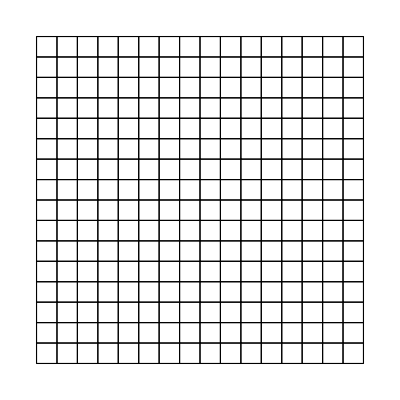

```mathematica
Unprotect[λ,μ,Subscript[ρ, 0],Subscript[ρ, 1],Subscript[ζ, 0],Subscript[ζ, 1],Ω^h,α, αΔT];
ClearAll[λ,μ,Subscript[ρ, 0],Subscript[ρ, 1],Subscript[ζ, 0],Subscript[ζ, 1],Ω^h,α, αΔT];
λ=1; μ=1; 
Subscript[ρ, 0]=0.5;Subscript[ρ, 1]=1.0;
Subscript[ζ, 0]=0.0;Subscript[ζ, 1]=0.5;
L̄=(Subscript[ζ, 1]-Subscript[ζ, 0])/π;
αΔT[ρ_,ζ_]=ρ;
Ω^h=ToElementMesh[Rectangle[{Subscript[ρ, 0],Subscript[ζ, 0]},{Subscript[ρ, 1],Subscript[ζ, 1]}],MaxCellMeasure->0.001,"MeshElementType"->"QuadElement","MeshOrder"->2]
Protect[λ,μ,Subscript[ρ, 0],Subscript[ρ, 1],Subscript[ζ, 0],Subscript[ζ, 1],Ω^h,α,αΔT];
(Ω^h)["Wireframe"]
AutoCollapse[]
```

```mathematica
Unprotect[Subscript[n, np],Subscript[n, en],Subscript[n, el],Subscript[n, dof],Subscript[n, guass],Subscript[η, g],Subscript[n, eq],IEN,ID,ElementMesh,NMat];
ClearAll[Subscript[n, np],Subscript[n, en],Subscript[n, el],Subscript[n, dof],Subscript[n, guass],Subscript[η, g],Subscript[n, eq],IEN,ID,(*ElementMesh,*)NMat];
(x⃗)^h=(Ω^h)["Coordinates"];
Subscript[n, np]=Length@((x⃗)^h);
IEN=Apply[List,(Ω^h)["MeshElements"],{1}][[1,1]]ᵀ ;
NMat[ξ_,η_]={(N^(1))[ξ,η],(N^(2))[ξ,η],(N^(3))[ξ,η],(N^(4))[ξ,η],(N^(5))[ξ,η],(N^(6))[ξ,η],(N^(7))[ξ,η],(N^(8))[ξ,η]};
Subscript[n, en]=Dimensions[IEN][[1]];
Subscript[n, el]=Dimensions[IEN][[2]];
Subscript[n, dof]=3;
Subscript[n, guass]=9;
Subscript[η, g]=Subscript[SetUpη, g][(x⃗)^h] ;
ID=SetUpIDArray[];
Subscript[n, eq]=Max[ID];
(Ω^h)["PointElements"]={PointElement[Table[{i},{i,1,Subscript[n, np]}]]};
Protect[Subscript[n, np],Subscript[n, en],Subscript[n, el],Subscript[n, dof],Subscript[n, guass],Subscript[η, g],Subscript[n, eq],IEN,ID,ElementMesh, NMat];
AutoCollapse[]
```

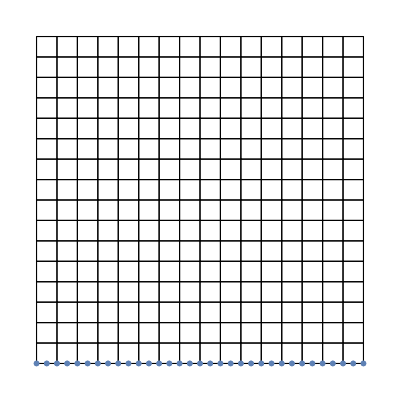

```mathematica
Show[
(Ω^h)["Wireframe"(*["MeshElement" -> "MeshElements","MeshElementIDStyle"->Blue]],
Ω^h["Wireframe"["MeshElement" -> "PointElements","MeshElementIDStyle"->Red]*)],
ListPlot[((x⃗)^h)[[Subscript[η, g][[1]]]],PlotMarkers->{Yellow,Large}],ListPlot[((x⃗)^h)[[Subscript[η, g][[2]]]],PlotMarkers->{Green}],ListPlot[((x⃗)^h)[[Subscript[η, g][[3]]]],PlotMarkers->{\[FreakedSmiley],Large}]]
AutoCollapse[]
```

### Solve

```mathematica
ParallelEvaluate[$KernelID];
DistributeDefinitions[ComputeElementStiffnessMatrix,GuassIntegrate,ElementJacobian,CalculateGuassPoints,IEN,ID,λ,μ,k^e,f^e,NMat,ComputeElementStiffnessMatrixForStressProjection,ComputeGlobalForceMatrix,ComputeGlobalForceMatrixForStressProjection,ComputeGlobalForceMatrixForStressProjection];
Clear[KMat,fMat];
ParallelEvaluate[KMat=SparseArray[{},{Subscript[n, eq],Subscript[n, eq]},0.0];];
ParallelEvaluate[fMat=SparseArray[{},{Subscript[n, eq]},0.0]];
ParallelMap[ComputeElementStiffnessMatrix,Range[Subscript[n, el]]]//AbsoluteTiming;
ParallelMap[ComputeGlobalForceMatrix,Range[Subscript[n, el]]]//AbsoluteTiming;

KMatP =Total@ParallelEvaluate[KMat];
fMatP =Total@ParallelEvaluate[fMat];
t1 = AbsoluteTime[];
sol1=LinearSolve[KMatP,fMatP];
t2 = AbsoluteTime[]-t1;
UMat=SplitSolution[sol1];
{Subscript[Un, 1],Subscript[Un, 2],Subscript[Un, 3]}=Table[ElementMeshInterpolation[{Ω^h}, UMat[[i,;;]]//Normal],{i,1,Subscript[n, dof]}];
```

### Post-processing

#### Computing derivatives for u^ρ, u^ϕ , u^ζ w.r.t {ρ, ζ}

```mathematica
ClearAll[aMat,l11Mat,l13Mat,l21Mat,l23Mat,l31Mat,l33Mat];
ParallelEvaluate[aMat=SparseArray[{},{Subscript[n, np],Subscript[n, np]},0.0];];
ParallelEvaluate[l11Mat=l13Mat=l21Mat=l23Mat=l31Mat=l33Mat= SparseArray[{},{Subscript[n, np]},0.0]];
ParallelMap[ComputeElementStiffnessMatrixForStressProjection,Range[Subscript[n, el]]]//AbsoluteTiming;
ParallelMap[ComputeGlobalForceMatrixForStressProjection,Range[Subscript[n, el]]]//AbsoluteTiming;
aMatP=Total@ParallelEvaluate[aMat];
l11MatP=Total@ParallelEvaluate[l11Mat];
l13MatP=Total@ParallelEvaluate[l13Mat];
l21MatP =Total@ParallelEvaluate[l21Mat];
l23MatP =Total@ParallelEvaluate[l23Mat];
l31MatP =Total@ParallelEvaluate[l31Mat];
l33MatP =Total@ParallelEvaluate[l33Mat];
```

```mathematica
ClearAll[sol,U11,U13,U21,U23,U31,U33];
t1 = AbsoluteTime[];
aMatInv=LinearSolve[aMatP];
{U11,U13,U21,U23,U31,U33}=ElementMeshInterpolation[{Ω^h},#] & /@ (aMatInv[#]&/@{l11MatP,l13MatP,l21MatP,l23MatP,l31MatP,l33MatP});
t2 = AbsoluteTime[] - t1
```

#### Computing Stress and strain

```mathematica
((U⃗)^n)[χ__] := {Subscript[Un, 1]@@χ,Subscript[Un, 2]@@χ,Subscript[Un, 3]@@χ};
X⃗ = {ρ,ϕ,ζ};
Subscript[X⃗, r] = {ρ,ζ};
Subscript[U⃗, n][χ__]:= {g_(1·1·)Subscript[Un, 1]@@χ +g_(1·2·)Subscript[Un, 2]@@χ +g_(1·3·)Subscript[Un, 3]@@χ  ,g_(2·1·)Subscript[Un, 1]@@χ +g_(2·2·)Subscript[Un, 2]@@χ  +g_(2·3·)Subscript[Un, 3]@@χ ,g_(3·1·)Subscript[Un, 1]@@χ +g_(3·2·)Subscript[Un, 2]@@χ  +g_(3·3·)Subscript[Un, 3]@@χ} 
Subscript[γ, n][ρ_,ζ_] =  1/2 Table[D[Subscript[U⃗, n][Subscript[X⃗, r]][[i]],{X⃗[[j]],1}]-  ∑_(k=1)^3 Subscript[U⃗, n][Subscript[X⃗, r]][[k]] Γ_(i·j·)^(k·)+ D[Subscript[U⃗, n][Subscript[X⃗, r]][[j]],{X⃗[[i]],1}]-  ∑_(k=1)^3 Subscript[U⃗, n][Subscript[X⃗, r]][[k]] Γ_(j·i·)^(k·),{i,1,3},{j,1,3}];
(τ^n)[ρ_,ζ_] = Table[∑_(k=1)^3 ∑_(l=1)^3 𝔼^(i·j·k·l·)(Subscript[γ, n][ρ,ζ][[k,l]]-αΔT[ρ,ζ] g_(k·l·)),{i,1,3},{j,1,3}];
```

```mathematica
{(Subscript[u, h]^ρ)[χ__],(Subscript[u, h]^ϕ)[χ__],(Subscript[u, h]^ζ)[χ__]} := {Subscript[Un, 1]@@χ,Subscript[Un, 2]@@χ,Subscript[Un, 3]@@χ};
{(Subscript[u, ρ]^h)[χ__],(Subscript[u, ϕ]^h)[χ__],(Subscript[u, ζ]^h)[χ__]} := {g_(1·1·)Subscript[Un, 1]@@χ +g_(1·2·)Subscript[Un, 2]@@χ +g_(1·3·)Subscript[Un, 3]@@χ  ,g_(2·1·)Subscript[Un, 1]@@χ +g_(2·2·)Subscript[Un, 2]@@χ  +g_(2·3·)Subscript[Un, 3]@@χ ,g_(3·1·)Subscript[Un, 1]@@χ +g_(3·2·)Subscript[Un, 2]@@χ  +g_(3·3·)Subscript[Un, 3]@@χ} ;
{(Subscript[u, h]^(ρ,ρ))[χ__],(Subscript[u, h]^(ϕ,ρ))[χ__],(Subscript[u, h]^(ζ,ρ))[χ__]}:= {U11@@χ,U21@@χ,U31@@χ};
{(Subscript[u, h]^(ρ,ζ))[χ__],(Subscript[u, h]^(ϕ,ζ))[χ__],(Subscript[u, h]^(ζ,ζ))[χ__]}:= {U13@@χ,U23@@χ,U33@@χ};
```

#### Given: (∂U^i)/(∂X_j). To Find: (∂U_i)/(∂X_j)?

```mathematica
Subscript[U, i] = Subscript[g, i k] U^k
(∂Subscript[U, i])/(∂Subscript[X, j]) = (∂Subscript[g, i k])/(∂Subscript[X, j])U^k + Subscript[g, i k] (∂U^k)/(∂Subscript[X, j])
```

```mathematica
(Subscript[u, ρ,ρ]^h)[ρ_,ζ_]= (∂g_(1·1·))/(∂ ρ)(Subscript[u, h]^ρ)[Subscript[X⃗, r]]+(∂g_(1·2·))/(∂ ρ)(Subscript[u, h]^ϕ)[Subscript[X⃗, r]]+(∂g_(1·3·))/(∂ ρ)(Subscript[u, h]^ζ)[Subscript[X⃗, r]]+ g_(1·1·)(Subscript[u, h]^(ρ,ρ))[Subscript[X⃗, r]] +  g_(1·2·)(Subscript[u, h]^(ϕ,ρ))[Subscript[X⃗, r]]+g_(1·3·)(Subscript[u, h]^(ζ,ρ))[Subscript[X⃗, r]];
(Subscript[u, ϕ,ρ]^h)[ρ_,ζ_]= (∂g_(2·1·))/(∂ ρ)(Subscript[u, h]^ρ)[Subscript[X⃗, r]]+(∂g_(2·2·))/(∂ ρ)(Subscript[u, h]^ϕ)[Subscript[X⃗, r]]+(∂g_(2·3·))/(∂ ρ)(Subscript[u, h]^ζ)[Subscript[X⃗, r]]+ g_(2·1·)(Subscript[u, h]^(ρ,ρ))[Subscript[X⃗, r]] +  g_(2·2·)(Subscript[u, h]^(ϕ,ρ))[Subscript[X⃗, r]]+g_(2·3·)(Subscript[u, h]^(ζ,ρ))[Subscript[X⃗, r]];
(Subscript[u, ζ,ρ]^h)[ρ_,ζ_]= (∂g_(3·1·))/(∂ ρ)(Subscript[u, h]^ρ)[Subscript[X⃗, r]]+(∂g_(3·2·))/(∂ ρ)(Subscript[u, h]^ϕ)[Subscript[X⃗, r]]+(∂g_(3·3·))/(∂ ρ)(Subscript[u, h]^ζ)[Subscript[X⃗, r]]+ g_(3·1·)(Subscript[u, h]^(ρ,ρ))[Subscript[X⃗, r]] +  g_(3·2·)(Subscript[u, h]^(ϕ,ρ))[Subscript[X⃗, r]]+g_(3·3·)(Subscript[u, h]^(ζ,ρ))[Subscript[X⃗, r]];
(Subscript[u, ρ,ζ]^h)[ρ_,ζ_]= (∂g_(1·1·))/(∂ ζ)(Subscript[u, h]^ρ)[Subscript[X⃗, r]]+(∂g_(1·2·))/(∂ ζ)(Subscript[u, h]^ϕ)[Subscript[X⃗, r]]+(∂g_(1·3·))/(∂ ζ)(Subscript[u, h]^ζ)[Subscript[X⃗, r]]+ g_(1·1·)(Subscript[u, h]^(ρ,ζ))[Subscript[X⃗, r]] +  g_(1·2·)(Subscript[u, h]^(ϕ,ζ))[Subscript[X⃗, r]]+g_(1·3·)(Subscript[u, h]^(ζ,ζ))[Subscript[X⃗, r]];
(Subscript[u, ϕ,ζ]^h)[ρ_,ζ_]= (∂g_(2·1·))/(∂ ζ)(Subscript[u, h]^ρ)[Subscript[X⃗, r]]+(∂g_(2·2·))/(∂ ζ)(Subscript[u, h]^ϕ)[Subscript[X⃗, r]]+(∂g_(2·3·))/(∂ ζ)(Subscript[u, h]^ζ)[Subscript[X⃗, r]]+ g_(2·1·)(Subscript[u, h]^(ρ,ζ))[Subscript[X⃗, r]] +  g_(2·2·)(Subscript[u, h]^(ϕ,ζ))[Subscript[X⃗, r]]+g_(2·3·)(Subscript[u, h]^(ζ,ζ))[Subscript[X⃗, r]];
(Subscript[u, ζ,ζ]^h)[ρ_,ζ_]= (∂g_(3·1·))/(∂ ζ)(Subscript[u, h]^ρ)[Subscript[X⃗, r]]+(∂g_(3·2·))/(∂ ζ)(Subscript[u, h]^ϕ)[Subscript[X⃗, r]]+(∂g_(3·3·))/(∂ ζ)(Subscript[u, h]^ζ)[Subscript[X⃗, r]]+ g_(3·1·)(Subscript[u, h]^(ρ,ζ))[Subscript[X⃗, r]] +  g_(3·2·)(Subscript[u, h]^(ϕ,ζ))[Subscript[X⃗, r]]+g_(3·3·)(Subscript[u, h]^(ζ,ζ))[Subscript[X⃗, r]];
```

#### U_(i |_j) = (∂U_i)/(∂X_j) - Γ_(i j)^k U_k

```mathematica
CovarDuh[ρ_,ζ_]= {{(Subscript[u, ρ,ρ]^h)[ρ,ζ] -(Γ_(1·1·)^(1·)(Subscript[u, ρ]^h)[{ρ,ζ}]+Γ_(1·1·)^(2·)(Subscript[u, ϕ]^h)[{ρ,ζ}]+ Γ_(1·1·)^(3·)(Subscript[u, ζ]^h)[{ρ,ζ}]),-(Γ_(1·2·)^(1·)(Subscript[u, ρ]^h)[{ρ,ζ}]+Γ_(1·2·)^(2·)(Subscript[u, ϕ]^h)[{ρ,ζ}]+ Γ_(1·2·)^(3·)(Subscript[u, ζ]^h)[{ρ,ζ}]),(Subscript[u, ρ,ζ]^h)[ρ,ζ] -(Γ_(1·3·)^(1·)(Subscript[u, ρ]^h)[{ρ,ζ}]+Γ_(1·3·)^(2·)(Subscript[u, ϕ]^h)[{ρ,ζ}]+ Γ_(1·3·)^(3·)(Subscript[u, ζ]^h)[{ρ,ζ}])},{(Subscript[u, ϕ,ρ]^h)[ρ,ζ] -(Γ_(2·1·)^(1·)(Subscript[u, ρ]^h)[{ρ,ζ}]+Γ_(2·1·)^(2·)(Subscript[u, ϕ]^h)[{ρ,ζ}]+ Γ_(2·1·)^(3·)(Subscript[u, ζ]^h)[{ρ,ζ}]),-(Γ_(2·2·)^(1·)(Subscript[u, ρ]^h)[{ρ,ζ}]+Γ_(2·2·)^(2·)(Subscript[u, ϕ]^h)[{ρ,ζ}]+ Γ_(2·2·)^(3·)(Subscript[u, ζ]^h)[{ρ,ζ}]),(Subscript[u, ϕ,ζ]^h)[ρ,ζ] -(Γ_(2·3·)^(1·)(Subscript[u, ρ]^h)[{ρ,ζ}]+Γ_(2·3·)^(2·)(Subscript[u, ϕ]^h)[{ρ,ζ}]+ Γ_(2·3·)^(3·)(Subscript[u, ζ]^h)[{ρ,ζ}])},{(Subscript[u, ζ,ρ]^h)[ρ,ζ] -(Γ_(3·1·)^(1·)(Subscript[u, ρ]^h)[{ρ,ζ}]+Γ_(3·1·)^(2·)(Subscript[u, ϕ]^h)[{ρ,ζ}]+ Γ_(3·1·)^(3·)(Subscript[u, ζ]^h)[{ρ,ζ}]),-(Γ_(3·2·)^(1·)(Subscript[u, ρ]^h)[{ρ,ζ}]+Γ_(3·2·)^(2·)(Subscript[u, ϕ]^h)[{ρ,ζ}]+ Γ_(3·2·)^(3·)(Subscript[u, ζ]^h)[{ρ,ζ}]),(Subscript[u, ζ,ζ]^h)[ρ,ζ] -(Γ_(3·3·)^(1·)(Subscript[u, ρ]^h)[{ρ,ζ}]+Γ_(3·3·)^(2·)(Subscript[u, ϕ]^h)[{ρ,ζ}]+ Γ_(3·3·)^(3·)(Subscript[u, ζ]^h)[{ρ,ζ}])}};
```

#### CovarStrain (γ_(i j)) = 1/2(U_(i |_j) + U_(j |_i)) ContravariantStress (τ^(i j)) = Ε^(i j k l) (γ_(k l) -αΔTg_(k l))

```mathematica
CovarStrain[ρ_,ζ_] = 1/2 Table[CovarDuh[ρ,ζ][[i,j]]+CovarDuh[ρ,ζ][[j,i]],{i,1,3},{j,1,3}];
ContravarStress[ρ_,ζ_] = Table[∑_(k=1)^3 ∑_(l=1)^3 𝔼^(i·j·k·l·)(CovarStrain[ρ,ζ][[k,l]]-αΔT[ρ,ζ] g_(k·l·)),{i,1,3},{j,1,3}];
CovarStress[ρ_,ζ_] =Table[∑_(k=1)^3 ∑_(l=1)^3 ContravarStress[ρ,ζ][[k,l]] g_(i·k·)g_(j·l·),{i,1,3},{j,1,3}];
```

#### Compute the total energy

```mathematica
Echo[1/2 NIntegrate[∑_(k=1)^3 ∑_(l=1)^3 ContravarStress[ρ,ζ][[k,l]](CovarStrain[ρ,ζ][[k,l]]-αΔT[ρ,ζ] g_(k·l·))ρ,{ρ,ζ}∈ Ω^h],"Energy, Method 1 (using postprocessing) "];
Echo[1/2 NIntegrate[∑_(k=1)^3 ∑_(l=1)^3 ContravarStress[ρ,ζ][[k,l]](-αΔT[ρ,ζ] g_(k·l·))ρ,{ρ,ζ}∈ Ω^h],"Energy, Method 2 (using postprocessing)"];
```

```mathematica
(Subscript[σ, ρ]^ρ)[ρ_,ζ_] = ∑_(k=1)^3 ContravarStress[ρ,ζ][[k,1]] g_(k·1·);
(Subscript[σ, ϕ]^ρ)[ρ_,ζ_] = ∑_(k=1)^3 ContravarStress[ρ,ζ][[k,1]] g_(k·2·);
(Subscript[σ, ζ]^ρ)[ρ_,ζ_] = ∑_(k=1)^3 ContravarStress[ρ,ζ][[k,1]] g_(k·3·);
(Subscript[σ, ρ]^ζ)[ρ_,ζ_] =∑_(k=1)^3 ContravarStress[ρ,ζ][[k,3]] g_(k·1·);
(Subscript[σ, ϕ]^ζ)[ρ_,ζ_] = ∑_(k=1)^3 ContravarStress[ρ,ζ][[k,3]] g_(k·2·);
(Subscript[σ, ζ]^ζ)[ρ_,ζ_] = ∑_(k=1)^3 ContravarStress[ρ,ζ][[k,3]] g_(k·3·);
```

### Visualize Results

#### Show Displacement Field

```mathematica
ContourPlot[Subscript[Un, 1][ρ,ζ],{ρ,ζ}∈Ω^h,ColorFunction->"Temperature",AspectRatio->1,PlotLegends->Automatic,PlotRange->All]
ContourPlot[Subscript[Un, 2][ρ,ζ],{ρ,ζ}∈Ω^h,ColorFunction->"Temperature",AspectRatio->1,PlotLegends->Automatic,PlotRange->All]
ContourPlot[Subscript[Un, 3][ρ,ζ],{ρ,ζ}∈Ω^h,ColorFunction->"Temperature",AspectRatio->1,PlotLegends->Automatic,PlotRange->All]
```

#### Verify boundary conditions

```mathematica
Plot[{Subscript[Un, 2][ρ,Subscript[ζ, 0]],Subscript[Un, 3][ρ,Subscript[ζ, 0]]},{ρ,Subscript[ρ, 0],Subscript[ρ, 1]},PlotStyle->{{Red,Dashed},{Blue,Opacity[0.25]}},PlotLegends->{"u^ϕ","u^ζ"}]
```

#### Traction free boundary checks

```mathematica
Plot[{(Subscript[σ, ρ]^ρ)[ρ,Subscript[ζ, 1]/5],(Subscript[σ, ρ]^ρ)[ρ,Subscript[ζ, 1]/2],(Subscript[σ, ρ]^ρ)[ρ,Subscript[ζ, 1]/1.2],(τ^n)[ρ,Subscript[ζ, 1]/5][[1,1]]},{ρ,Subscript[ρ, 0],Subscript[ρ, 1]},PlotRange->All,PlotStyle->{{Red,Thickness->0.01,Opacity[0.5]},{Blue,Dashed,Thickness->0.01,Opacity[0.25]},{Black,Dashed,Thickness->0.01},{Green}},PlotLegends->{"σ_ρ^ρ|_(ζ = 1)","σ_ρ^ρ|_(ζ = 5)","σ_ρ^ρ|_(ζ = 9)"}]
```

```mathematica
Plot[{(Subscript[σ, ϕ]^ρ)[ρ,Subscript[ζ, 1]/5],(Subscript[σ, ϕ]^ρ)[ρ,Subscript[ζ, 1]/2],(Subscript[σ, ϕ]^ρ)[ρ,Subscript[ζ, 1]/1.2]},{ρ,Subscript[ρ, 0],Subscript[ρ, 1]},PlotRange->All,PlotStyle->{{Red,Thickness->0.01,Opacity[0.5]},{Blue,Dashed,Thickness->0.01,Opacity[0.25]},{Black,Dashed,Thickness->0.01},{Green}},PlotLegends->{"σ_ϕ^ρ|_(ζ = 1)","σ_ϕ^ρ|_(ζ = 5)","σ_ϕ^ρ|_(ζ = 9)"}]
```

Plot of Stress vs XX

```mathematica
Plot[{(Subscript[σ, ζ]^ρ)[ρ,Subscript[ζ, 1]/5],(Subscript[σ, ζ]^ρ)[ρ,Subscript[ζ, 1]/2],(Subscript[σ, ζ]^ρ)[ρ,Subscript[ζ, 1]/1.2]},{ρ,Subscript[ρ, 0],Subscript[ρ, 1]},PlotRange->All,PlotStyle->{{Red,Thickness->0.01,Opacity[0.5]},{Blue,Dashed,Thickness->0.01,Opacity[0.25]},{Black,Dashed,Thickness->0.01},{Green}},PlotLegends->{"σ_ζ^ρ|_(ζ = 1)","σ_ζ^ρ|_(ζ = 5)","σ_ζ^ρ|_(ζ = 9)"}]
(*alhdhckhkch*)
```

```mathematica
Plot[{(Subscript[σ, ρ]^ζ)[0.6,ζ],(Subscript[σ, ρ]^ζ)[0.75,ζ],(Subscript[σ, ρ]^ζ)[0.9,ζ]},{ζ,Subscript[ζ, 0],Subscript[ζ, 1]},PlotRange->All,PlotStyle->{{Red,Thickness->0.01,Opacity[0.5]},{Blue,Dashed,Thickness->0.01,Opacity[0.25]},{Black,Dashed,Thickness->0.01},{Green}},PlotLegends->{"σ_ρ^ζ|_(ρ = 0.6)","σ_ρ^ζ|_(ρ = 0.75)","σ_ρ^ζ|_(ρ = 0.9)"}]
```

```mathematica
Plot[{(Subscript[σ, ϕ]^ζ)[0.6,ζ],(Subscript[σ, ϕ]^ζ)[0.75,ζ],(Subscript[σ, ϕ]^ζ)[0.9,ζ]},{ζ,Subscript[ζ, 0],Subscript[ζ, 1]},PlotRange->All,PlotStyle->{{Red,Thickness->0.01,Opacity[0.5]},{Blue,Dashed,Thickness->0.01,Opacity[0.25]},{Black,Dashed,Thickness->0.01},{Green}},PlotLegends->{"σ_ϕ^ζ|_(ρ = 0.6)","σ_ϕ^ζ|_(ρ = 0.75)","σ_ϕ^ζ|_(ρ = 0.9)"}]
```

```mathematica
Plot[{(Subscript[σ, ζ]^ζ)[0.6,ζ],(Subscript[σ, ζ]^ζ)[0.75,ζ],(Subscript[σ, ζ]^ζ)[0.9,ζ]},{ζ,Subscript[ζ, 0],Subscript[ζ, 1]},PlotRange->All,PlotStyle->{{Red,Thickness->0.01,Opacity[0.5]},{Blue,Dashed,Thickness->0.01,Opacity[0.25]},{Black,Dashed,Thickness->0.01},{Green}},PlotLegends->{"σ_ζ^ζ|_(ρ = 0.6)","σ_ζ^ζ|_(ρ = 0.75)","σ_ζ^ζ|_(ρ = 0.9)"}]
```